# Иваненко Иван, Лабораторная работы # 2

## Задание 1 1.1 Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением. Последовательно примените к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify и объясните их действия.

```mathematica
(*Expand раскрывает скобки и возводит выражение в положтельную степень*)
```

```mathematica
exp = (5 (a^3-b^3))/((4 a+2) (a+b^2))+a^4-b^4+3(a - b)^2;
Expand[exp]
```

3 a^2+a^4-6 a b+3 b^2-b^4+(5 a^3)/((2+4 a) (a+b^2))-(5 b^3)/((2+4 a) (a+b^2))

```mathematica
(*ExpandAll раскрывает все скобки и возводит в положительную степень все части выражения*)
```

```mathematica
ExpandAll[exp]
```

3 a^2+a^4-6 a b+3 b^2-b^4+(5 a^3)/(2 a+4 a^2+2 b^2+4 a b^2)-(5 b^3)/(2 a+4 a^2+2 b^2+4 a b^2)

```mathematica
(*Из официальной документации: Factor факторизирует полином над целыми числами.*)
```

```mathematica
Factor[exp]
```

((a-b) (11 a^2+12 a^3+2 a^4+4 a^5-a b-12 a^2 b+2 a^3 b+4 a^4 b+5 b^2+6 a b^2+14 a^2 b^2+6 a^3 b^2+4 a^4 b^2-6 b^3-10 a b^3+6 a^2 b^3+4 a^3 b^3+2 a b^4+4 a^2 b^4+2 b^5+4 a b^5))/(2 (1+2 a) (a+b^2))

```mathematica
(*Из официальной документации: Together складывает члены в сумму по общему знаменателю и отменяет множители в результате.*)
```

```mathematica
Together[exp]
```

(11 a^3+12 a^4+2 a^5+4 a^6-12 a^2 b-24 a^3 b+6 a b^2+18 a^2 b^2+12 a^3 b^2+2 a^4 b^2+4 a^5 b^2-5 b^3-12 a b^3-24 a^2 b^3+6 b^4+10 a b^4-4 a^2 b^4-2 b^6-4 a b^6)/(2 (1+2 a) (a+b^2))

```mathematica
(*Из официальной документации: Apart переписывает рациональное выражение как сумму выражений с минимальными знаменателями.*)
```

```mathematica
Apart[exp]
```

a^2 (3+a^2)-((5+12 a+24 a^2) b)/(2 (1+2 a))+3 b^2-b^4+(5 (a^3+a b))/(2 (1+2 a) (a+b^2))

```mathematica
(*Из официальной документации: Cancel убирает общие множители в числителе и знаменателе выражения *)
```

```mathematica
Cancel[exp]
```

a^4+3 (a-b)^2-b^4+(5 (a^3-b^3))/(2 (1+2 a) (a+b^2))

```mathematica
(*Из официальной документации: Simplify выполняет последовательность алгебраических и других преобразований выражения и возвращает простейшую найденную форму.*)
```

```mathematica
Simplify[exp]
```

a^4+3 (a-b)^2-b^4+(5 (a^3-b^3))/((2+4 a) (a+b^2))

## 1.2 Приведите выражение к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect предсавьте выражение t2 в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных. Используйте функции Exponent и Coefficient.

```mathematica
numtor = Numerator[Together[exp]];
```

```mathematica
11 a^3+12 a^4+2 a^5+4 a^6-12 a^2 b-24 a^3 b+6 a b^2+18 a^2 b^2+12 a^3 b^2+2 a^4 b^2+4 a^5 b^2-5 b^3-12 a b^3-24 a^2 b^3+6 b^4+10 a b^4-4 a^2 b^4-2 b^6-4 a b^6
```

11 a^3+12 a^4+2 a^5+4 a^6-12 a^2 b-24 a^3 b+6 a b^2+18 a^2 b^2+12 a^3 b^2+2 a^4 b^2+4 a^5 b^2-5 b^3-12 a b^3-24 a^2 b^3+6 b^4+10 a b^4-4 a^2 b^4-2 b^6-4 a b^6

```mathematica
Collect[numtor, {a, b}]
```

4 a^6-5 b^3+6 b^4-2 b^6+a^4 (12+2 b^2)+a^5 (2+4 b^2)+a^3 (11-24 b+12 b^2)+a^2 (-12 b+18 b^2-24 b^3-4 b^4)+a (6 b^2-12 b^3+10 b^4-4 b^6)

```mathematica
Exponent[numtor, a]
```

6

```mathematica
Coefficient[numtor, a]
```

6 b^2-12 b^3+10 b^4-4 b^6

```mathematica
CoefficientList[numtor, a]
```

{-5 b^3+6 b^4-2 b^6,6 b^2-12 b^3+10 b^4-4 b^6,-12 b+18 b^2-24 b^3-4 b^4,11-24 b+12 b^2,12+2 b^2,2+4 b^2,4}

## Задание 2 1. С помощью функции D вычислите производную функции x^n * cos(x)

```mathematica
D[x^n Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

## 2. Вычислите следующие производные

```mathematica
D[a x^3+2 x^2,x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5 x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[ x^3 y^2+3 x^2,{x,3},{y,2}]
```

12

## 3. Используя функцию Integrate, вычислите интеграл

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

## 4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подинтегральными выражениями

```mathematica
integrand = x^3/(x^2+1);
```

```mathematica
x^3/(1+x^2)
```

x^3/(1+x^2)

```mathematica
integrationResult = Integrate[integrand,x];
```

```mathematica
x^2/2-1/2 Log[1+x^2]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
res = Together[D[integrationResult, x]]
```

x^3/(1+x^2)

```mathematica
integrand === res
```

True

```mathematica
integrand2 = 1/(x^3+1);
```

```mathematica
1/(1+x^3)
```

1/(1+x^3)

```mathematica
integrationResult2 = Integrate[integrand2, x];
```

```mathematica
ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
res2 = Simplify[D[integrationResult2, x]];
```

```mathematica
x^3/(1+x^2)
```

x^3/(1+x^2)

```mathematica
integrand2 === res2;
```

```mathematica
True
```

True

## 5. Вычислите определенный интеграл

```mathematica
Integrate[5*x-2*√x+32/x^3, {x,1,4}]
```

259/6

## 6. Вычислите интегралы

```mathematica
N[Integrate[(1+x^4)^(1/3), {x,0,1}],25]
```

1.057527731779011858114859

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

## Задание 3 1. Используя функцию Solve, решить уравнение

```mathematica
Solve[a*x^4 + x^2 + 3 == 0, x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

## 2. Найти точное решение системы уравнений

```mathematica
Solve[x^2 + y == 1 && y^2 - x^2 == 2, {x, y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

## 3. Решить систему уравнений. Если точное решение найти не удается, получите численное решение.

```mathematica
Solve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→5-(Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025)^3,y→Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025},{x→5-(Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715)^3,y→Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715},{x→5-(Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702)^3,y→Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702},{x→5-(Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702)^3,y→Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702},{x→5-(Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017)^3,y→Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017},{x→5-(Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017)^3,y→Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017}}

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y}, Reals]
```

{{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285}}

## 4. Найдите общие решения дифференциальных уравнений, используя функцию DSolve. Самостоятельно задайте граничные условия и найдите соответствующие им частные решения. Постройте их графики

```mathematica
result = DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
result2 = DSolve[y'[x]+y[x]*Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

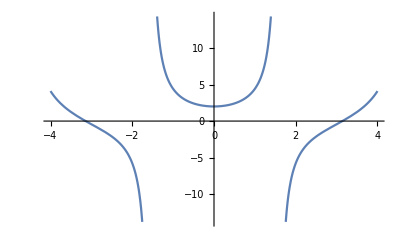

```mathematica
Plot[Evaluate[y[x]/. result /. {C[1] ->1}],{x,-4,4}]
```

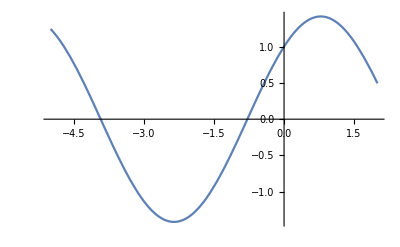

```mathematica
Plot[Evaluate[y[x]/. result2 /. {C[1] ->1}],{x,-5,2}]
```

## 5. Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде.

```mathematica
t3= DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==2, y'[0]==3}, y[x], x]//FullSimplify
```

{{y[x]→2 ⅇ^(x/2) π (-((AiryAi[1/4]+AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+AiryBiPrime[1/4]))}}

```mathematica
t4 = NDSolve[{y''[x]-y'[x]+x* y[x]==0, y[0]==2, y'[0]==3}, y[x], {x, -5,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

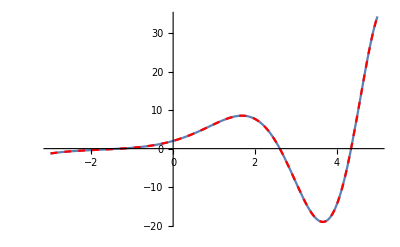

```mathematica
Show[Plot[t3[[1,1,2]],{x,-3,5}], Plot[t4[[1, 1, 2]], {x, -3, 5},PlotStyle->{Dashed, Red}]]
```